## ConvexHullVertices example

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.5 (6-Nov-2012)) loaded Fri 9 Nov 2012 04:39:40
using xCellerator 0.90 and XSSA 1204002

```mathematica
Needs["ComputationalGeometry`"]
```

Generate  random vertices to use as Voronoi Centers

```mathematica
r:=RandomReal[{0,100}]; 
vertices=Table[{r,r}, {100}];
```

The built in ConvexHull function gives the convex hull in a storage-efficient format.

```mathematica
v=ComputationalGeometry`ConvexHull[vertices]
```

{52,79,8,45,28,22,72,76,62,13,18}

get the vertices by indexing int vertices

```mathematica
vertices[[v]]
```

{{99.2123,0.81539},{97.952,85.0857},{94.7632,97.2696},{52.6763,98.2616},{9.3993,98.3922},{3.6185,79.2565},{0.728666,67.4636},{0.721786,46.1392},{15.0079,4.39533},{20.7295,3.50819},{74.9928,0.137528}}

Use ConvexHullVertices to calculate the vertex coordinates directly for plotting. It combines the last two steps together into a single step.

```mathematica
ch=ConvexHullVertices[vertices]
```

{{99.2123,0.81539},{97.952,85.0857},{94.7632,97.2696},{52.6763,98.2616},{9.3993,98.3922},{3.6185,79.2565},{0.728666,67.4636},{0.721786,46.1392},{15.0079,4.39533},{20.7295,3.50819},{74.9928,0.137528}}

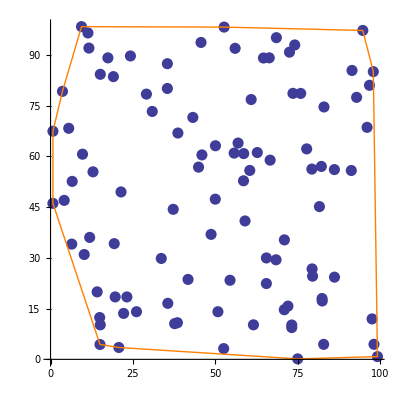

```mathematica
Show[ListPlot[vertices, PlotStyle-> {PointSize[.02]}], Boundary[ch,{Thick, Orange}], AspectRatio-> 1]
```